# 5. domača naloga

1.                                                                                                                                                                                         
V Mathematici predstavimo daljico v obliki Daljica[AA_, BB_], kjer sta AA in BB točki predstavljeni s parom koordinat v obliki {x, y}. Primer: 
d = Daljica[{-1, 1}, {3, -1}]

Sestavi naslednje funkcije:

	•Dolzina[Daljica[AA_, BB_]], ki vrne dolžino daljice.

	•EnacbaNosilke[Daljica[AA_, BB_]], ki vrne enačbo premice nosilke daljice. Primer, za daljico
	d kot zgoraj je enačba nosilke y == -x/2 + 1/2.

	•Slika[Daljica[AA_, BB_]], ki vrne grafični objekt Line, kateri predstavlja daljico.

	•Narisi[d__Daljica], ki za eno ali več podanih daljic le-te izriše

```mathematica
d = Daljica[{-1, 1},{3, -1}];
d2 = Daljica[{-1, -1}, {3, 1}];
d3 = Daljica[{-1, 2}, {3, 0}];
```

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Daljica[{-1,2},{3,0}]
```

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}];
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

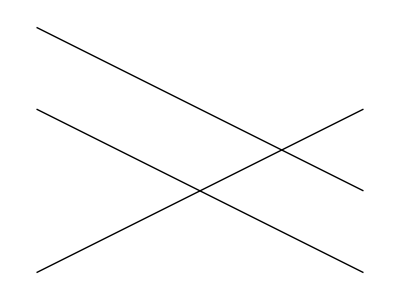

```mathematica
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
```

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

```mathematica
2.
```

Sestavi funkcijo Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]], ki vrne presečišče daljic, če
se sekata, oziroma prazen seznam ({}).

Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]]

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

3.                                                                                                                                         
Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik. Primer 

m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}] 

Ker gre za sklenjen mnogokotnik, predvidevamo, da ima ta povezave med zaporednimi točkami ter od
zadnje do prve točke. Sestavi naslednje funkcije:

	•Slika[Mnogokotnik[t__]], ki predstavi mnogokotnik s pomočjo grafičnega objekta Line. Naj-
	prej sestavi nov seznam točk, ki vključuje obstoječe točke mnogokotnika ter še ponovljeno prvo.
	Pozor: pazi, da ne izbrišeš obstoječe funkcije za sliko daljice!

	• Narisi[m__Mnogokotnik], ki nariše enega ali več mnogokotnikov. Pazi, pri risanju moraš narediti tudi daljico od zadnje do začetne točke. Premisli, kako iz obstoječega seznama točk sestaviš nov seznam, ki daljši za eno točko, t.j. ponovljeno prvo točko (Namig: funkciji Append 	ter First na seznamih.)

	•PravilniNKotnik[n_, r_], ki nariše pravilni n -kotnik s središčem v točki (0 , 0) in s točkami na krožnici z radijem r, pri čemer je ena točka v ( r, 0). Namig: uporabi funkcijo Table in upoštevaj, da se točke nahajajo na koordinatah ( r cos(( 2 π * i)/ n), r sin(( 2 π * i (/n ))) za i = 0 , . . . , n − 1.Izriši 
p5 = PravilniNKotnik[5, 2]
	
	•Nadgradi prejšnjo funkcijo v PravilniNKotnik[n_, r_, phi_], ki zgornji pravilni n-kotnik zavrti za kot phi. Premisli, kako je treba nadgraditi formulo za posamezno točko, da se premakne za kot phi. Rezultat uporabi v kombinaciji s funkcijo Manipulate in interaktivno demonstriraj rotacijo.
	
	•Daljice[Mnogokotnik[t__]], ki vrne seznam daljic, ki tvorijo mnogokotnik. Uporabi funkcijo Partition. V dokumentaciji preveri, kako deluje funkcija ter kako se uporablja zamikanje. Oglej si, 	kaj naredita naslednja ukaza:
	Partition[{1, 2, 3, 4, 5} , 2]
	Partition[{1, 2, 3, 4, 5} , 2, 1]

```mathematica
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
```

```mathematica
ClearAll [Slika, Narisi]
```

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

```mathematica
m = Append[m1, m1[[1]]];
Narisi[m__Mnogokotnik] := Graphics[Map[Slika, List[m]]]
```

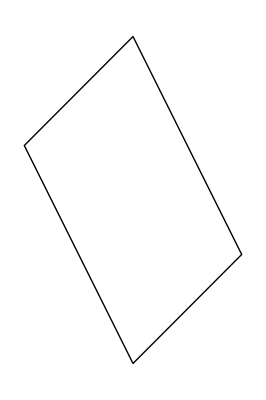

```mathematica
Narisi[m]
```

```mathematica
ClearAll[PravilniNKotnik, Narisi, i, n, r, p5]
```

```mathematica
p5 = PravilniNKotnik[5, 2];
```

```mathematica
Narisi[p5__PravilniNKotnik] := Graphics[{
	Line[
		Table[{p5[[2]] * Cos[(2*Pi * i) / p5[[1]]],
		p5[[2]] * Sin[(2*Pi * i) / p5[[1]]]}, {i, 0, p5[[1]]}]]}]
```

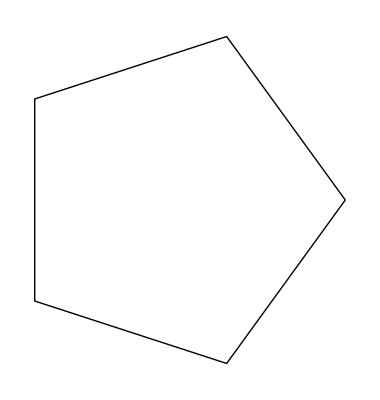

```mathematica
Narisi[p5]
```

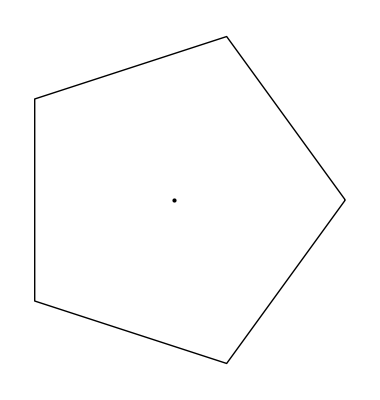

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n],r*Sin[(2 Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5=PravilniNKotnik[5,2]
```

```mathematica
p = PravilniNKotnik[5, 2, Pi];
```

```mathematica
Zavrti[p__PravilniNKotnik] := Manipulate[Graphics[{
	Line[
		Table[{p[[2]] * Cos[((2*Pi * i) / p[[1]]) + fi],
		 p[[2]] * Sin[((2*Pi * i) / p[[1]]) + fi]}, {i, 0, p[[1]]}]]}], 
			{fi, 0, p[[3]]}]
```

```mathematica
Zavrti[p]
```

4.                                                                                                                                       
Sestavi funkcijo Presek[m_Mnogokotnik, d_Daljica], ki izračuna presečišča mnogokotnika in
daljice. Pri tem uporabi že napisane funkcije ter pazi, da rezultat ne istih presečišč večkrat. Poskusi
uporabiti vgrajeni funkciji Select in DeleteDuplicates. Pomagaj si z naslednjimi primeri. Funkcijo
lahko definiramo tudi na naslednji način (namesto argumenta damo znak #, na koncu definicije pa
dodamo znak &.

aliJePrazen = Length[#] > 0 &

Primer uporabe:

aliJePrazen[{}]
False

aliJePrazen[{1, 2, 3}]
True

Potem jo pa lahko uporabimo kot preizkusno funkcijo za filtriranje neustreznih praznih seznamov:
Select[{{1, 2}, {}, {3, 4}, {}}, aliJePrazen]
{{1, 2}, {3, 4}}

```mathematica
ClearAll[d, d1, m1, m, seznamDaljic, Daljice]
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
d1 = Daljica[{-1,1},{3,-1}];
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
m = Append[m1, m1[[1]]]
seznamDaljic = Map[Daljica, Daljice[m]]
Daljice[Mnogokotnik[t__]] := Partition[{t},2,1]
Daljice[m]
Daljice1 = Partition[Flatten[Daljice[m]], 2, 2]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

Daljice[Daljica[Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]]]

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}},{{-1,2},{0,0}}}

{{0,0},{1,1},{1,1},{0,3},{0,3},{-1,2},{-1,2},{0,0}}

```mathematica
PresekBrezSeznama = Presek1[m__Mnogokotnik, d__Daljica] :=  
	For[i = 1, i <= Length[Daljice[m]], i++, Print[Presek[Daljica[Daljice[m][[i]][[1]], Daljice[m][[i]][[2]]], d]]]
```

```mathematica
Presek1[m, d1]
```

{1/3,1/3}

{}

{}

{-1/3,2/3}

```mathematica
PresekVSeznamu = {Presek1[m, d1]}
```

{1/3,1/3}

{}

{}

{-1/3,2/3}

```mathematica
{Null}
PresekVSez = List[Presek[m, d1]]
```

{Null}

{Presek[Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],Daljica[{-1,1},{3,-1}]]}

```mathematica
(*Kako se da presek v seznam? *)
```

```mathematica
aliJePrazen = Length[#] > 0 &;
```

```mathematica
aliJePrazen[{}]
```

False

```mathematica
aliJePrazen[{1, 2, 3}]
```

True

```mathematica
Select[{{1, 2}, {}, {3, 4}, {}}, aliJePrazen]
```

{{1,2},{3,4}}

```mathematica
Select[{{1/3,1/3},{}, {},{-1/3,2/3}},  aliJePrazen]
```

{{1/3,1/3},{-1/3,2/3}}

```mathematica
DeleteDuplicates[{{1/3,1/3},{}, {},{-1/3,2/3}}]
```

{{1/3,1/3},{},{-1/3,2/3}}

5.                                                                                                                   
5.Spodnja funkcija izračuna (uporabi) funkcijo f na vseh parih iz dveh seznamov.

VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]

VsiPari[f, {1, 2, 3}, {a, b}]
{f[1, a], f[1, b], f[2, a], f[2, b], f[3, a], f[3, b]}

	•Preuči, kaj točno naredita funkciji Outer in Flatten. Poglej v pomoč in preizkusi na primerih.
	
	•Sestavi funkcijo Presek[m1_Mnogokotnik, m2_Mnogokotnik], ki poišče presek dveh pravokotnikov. Uporabi funkcijo VsiPari.

```mathematica
VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]
```

```mathematica
VsiPari[f, {1, 2, 3}, {a, b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
Outer
Flatten
x = List[{0, 1,3}, {2, 3, 4}, {7,1}]
KajNarediFlatten = Flatten[x]
KajNarediOuter= Outer[f,x,x]
```

Outer

Flatten

{{0,1,3},{2,3,4},{7,1}}

{0,1,3,2,3,4,7,1}

{{{{f[0,0],f[0,1],f[0,3]},{f[0,2],f[0,3],f[0,4]},{f[0,7],f[0,1]}},{{f[1,0],f[1,1],f[1,3]},{f[1,2],f[1,3],f[1,4]},{f[1,7],f[1,1]}},{{f[3,0],f[3,1],f[3,3]},{f[3,2],f[3,3],f[3,4]},{f[3,7],f[3,1]}}},{{{f[2,0],f[2,1],f[2,3]},{f[2,2],f[2,3],f[2,4]},{f[2,7],f[2,1]}},{{f[3,0],f[3,1],f[3,3]},{f[3,2],f[3,3],f[3,4]},{f[3,7],f[3,1]}},{{f[4,0],f[4,1],f[4,3]},{f[4,2],f[4,3],f[4,4]},{f[4,7],f[4,1]}}},{{{f[7,0],f[7,1],f[7,3]},{f[7,2],f[7,3],f[7,4]},{f[7,7],f[7,1]}},{{f[1,0],f[1,1],f[1,3]},{f[1,2],f[1,3],f[1,4]},{f[1,7],f[1,1]}}}}

```mathematica
y = List[{1, 2}, {3, 5}]
```

{{1,2},{3,5}}

```mathematica
Flatten[y]
```

{1,2,3,5}

```mathematica
Outer[f, y, y]
```

{{{{f[1,1],f[1,2]},{f[1,3],f[1,5]}},{{f[2,1],f[2,2]},{f[2,3],f[2,5]}}},{{{f[3,1],f[3,2]},{f[3,3],f[3,5]}},{{f[5,1],f[5,2]},{f[5,3],f[5,5]}}}}

Flattern vzame gnezden seznam in vsak element zapiše v nov seznam, ki ni gnezden.
Outer naredi seznam vseh možnosti vgnezdenih seznamov, pri čemer je prvi element funkcija oziroma operator, druga dva elementa pa sta seznama.

```mathematica
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
```

```mathematica
m2 = Mnogokotnik[{0,1}, {2, 0}, {3, 1}, {1, 4}];
```

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:=
For[j = 1, j ≤Length[Daljice[m2]], j++, 
For[i=1, i<Length[Daljice[m1]], i++,
Print[Presek[Daljica[Daljice[m1][[i]][[1]], Daljice[m1][[i]][[2]]],
 Daljica[Daljice[m2][[i]][[1]], Daljice[m2][[i]][[2]]]]]]]

Presek[m1, m2]
```

{2/3,2/3}

{}

{2/3,2/3}

{}

{2/3,2/3}

{}

```mathematica
DeleteDuplicates[{{2/3,2/3}, {}, {2/3,2/3}, {}, {2/3,2/3}, {}}]
```

{{2/3,2/3},{}}

6.                                                                                                                  
 Izberi eno izmed nalog iz snovi pri linearni algebri in jo reši. Opiši potek in čim več računskega dela prepusti Mathematici. Če je možno, rezultate predstavi še grafično.

Izračunaj vektorski produkt vektorjev e1 = (2,1,1) in e2=(3,3,0), njuno vsoto ter razliko.
Podani sta točki T1 = (1, 1, 1) in T2 = (1, 2, 3). Zapiši smerni vektor premice, ki gre skozi točki T1 in T2. Nariši vektorje od T1 do T2 in vektorja e1 in e2 v 3D prostoru.

```mathematica
ClearAll[x, y, z]
```

```mathematica
T1=Tocka[1,1,1];
T2 = Tocka[1, 2, 3];
e1=Vektor[2,1,1];
e2=Vektor[3,3,0];
```

```mathematica
VektorskiProdukt[u_Vektor,v_Vektor]:=Vektor@@(List@@u×List@@v)
VektorskiProdukt[e1, e2]
```

Vektor[-3,3,3]

```mathematica
Vsota[u_Vektor,v_Vektor]:=Vektor@@(List@@u+List@@v)
Veckratnik[t_,u_Vektor]:=Vektor@@(t List@@u)
e3 = Vsota[e1, e2]
```

Vektor[5,4,1]

```mathematica
Razlika[u_Vektor,v_Vektor]:=Vsota[u,Veckratnik[-1,v]]
e4  =Razlika[e1, e2]
```

Vektor[-1,-2,1]

```mathematica
Tocka[u_Vektor]:=Tocka@@u
```

```mathematica
Vektor[A_Tocka,B_Tocka]:=Razlika[Vektor@@ B,Vektor@@A]
Vektor[T1, T2]
```

Vektor[0,1,2]

```mathematica
vektorji = {{List @@T1, List @@T2},{List @@T1, List @@e1},{List @@T1, List @@e2}}
```

{{{1,1,1},{1,2,3}},{{1,1,1},{2,1,1}},{{1,1,1},{3,3,0}}}

```mathematica
Graphics3D[Map[Line, vektorji ]]
```

-Graphics3D-